```mathematica
sol=Solve[r*x+4 x^3-9 x^5==0,x}
```

{x→0,x→-1/3 √(2-√(4+9 r)),x→1/3 √(2-√(4+9 r)),x→-1/3 √(2+√(4+9 r)),x→1/3 √(2+√(4+9 r))}

```mathematica
p1=Plot[sol⟦1,2⟧,{r,-1,0},PlotStyle->Blue]
```

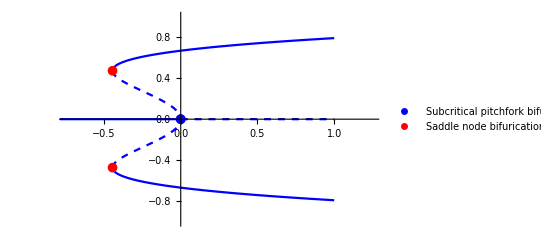

```mathematica
p2=Plot[sol⟦1,2⟧,{r,0,1},PlotStyle->{Blue,Dashed}];
p3=Plot[sol⟦2,2⟧,{r,-1,1},PlotStyle->{Blue,Dashed}];
p4=Plot[sol⟦3,2⟧,{r,-1,1},PlotStyle->{{Blue,Dashed},Blue}];
p5=Plot[sol⟦4,2⟧,{r,-1,1},PlotStyle->Blue];
p6=Plot[sol⟦5,2⟧,{r,-1,1},PlotStyle->Blue];
p7=ListPlot[{{0,0}},PlotMarkers->{Automatic,10},PlotStyle->Blue,PlotLegends->{"Subcritical pitchfork bifurcation"}];
p8 = ListPlot[{{-4/9, Sqrt[2]/3}, {-4/9, -Sqrt[2]/3}},PlotMarkers->{Automatic,10},PlotStyle->Red,PlotLegends->{"Saddle node bifurication"}];
Show[p1,p2,p3,p4,p5,p6,p7,p8, Axes->{False,True}, PlotRange -> {{-0.75, 1.25}, {-1, 1}}]
```